#### 4.3 Hahnfeldt Model with Periodic Anti-Angiogenic Treatment

```mathematica
Quit[];
```

```mathematica
p0=3000;q0=5000;α=0.2;β=0.15;μ=0.02;d=0.0087;b=2.3;
```

```mathematica
sol=NDSolve[{p'[t]==α*p[t]*Log[p[t]/q[t]],q'[t]==b*p[t]-(μ+d*p[t]^(2/3))*q[t]-(Sum[HeavisideTheta[t-(2*j-1)]- HeavisideTheta[t-(2*j)],{j,1,20}])*q[t],p[0]==p0,q[0]==q0},{p,q},{t,0,20}]
```

{{p→InterpolatingFunction[…],q→InterpolatingFunction[…]}}

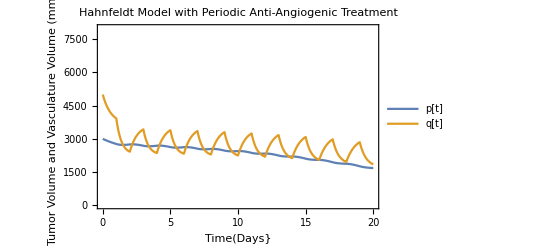

```mathematica
graph=Plot[Evaluate[{p[t],q[t]}/.sol],{t,0,20},PlotRange->{0,8000},ExclusionsStyle->Dashed,Frame->{True,True,False,False},PlotLabel->"Hahnfeldt Model with Periodic Anti-Angiogenic Treatment",FrameLabel->{"Time(Days}","Tumor Volume and Vasculature Volume (mm^3)"},PlotLegends->LineLegend[{"p[t]","q[t]"}]]
```

```mathematica
Export["/Users/robbiemead/Documents/Graduate School/Courses/Spring 2022/MATH 594/MATH 594 Project/hahnfeldt periodic treatment.pdf",graph]
```

/Users/robbiemead/Documents/Graduate School/Courses/Spring 2022/MATH 594/MATH 594 Project/hahnfeldt periodic treatment.pdf